### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={100,500,500}; (*мощности слоев*)
slopes = {0Degree, -0.9 Degree, -0.3 Degree, 2 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

type = -1 ;
listV = {1500,2000,2300,2500, 2800}; (*набор скоростей!!!больше на 1-2 чем горизонтов*)
```

```mathematica
(*folding parametres *)
hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)
gaussRadius = 5; (*start filter radius for GaussianFilter*)
```

```mathematica
velocityTrend = {0,1,1,1,1};(*1 or 0*)
velocityAnomaly ={1,0,0,0,0}; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "random"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["horizons"]];
table = BuildDepthSection[listH, slopes, len, dx, type, hDispersion, hTapering, gaussRadius][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
(*PlotVelocity[velModel, horizons]*)
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[73.2696+3076.86 t],FittedModel[265.23+2904.17 t],FittedModel[700.543+2617.04 t],FittedModel[1837.16+1692.74 t]}

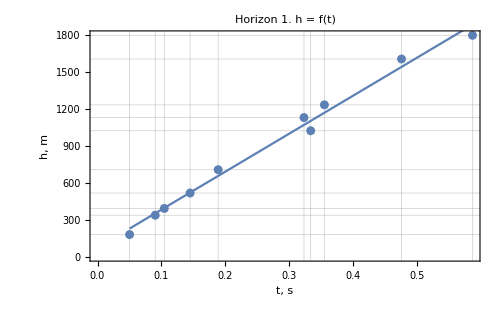
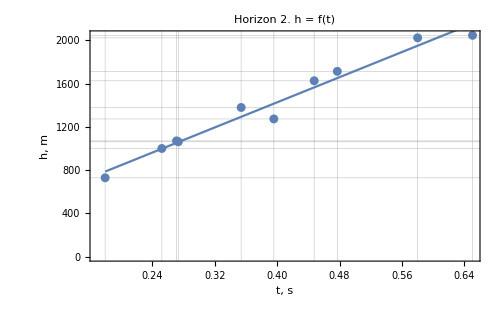
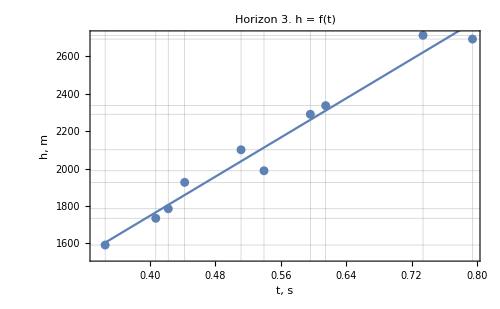
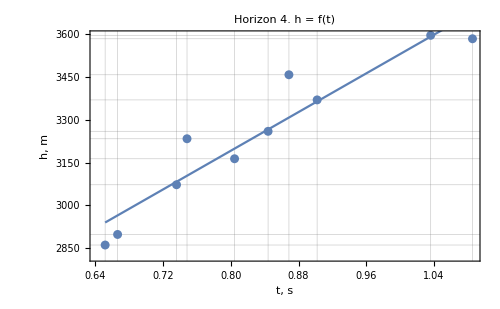

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[3768.88-1113.24 t],FittedModel[4381.16-1797.47 t],FittedModel[5287.07-2386.21 t],FittedModel[6047.95-2512.52 t]}

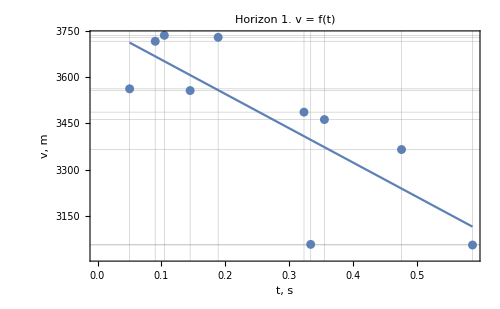
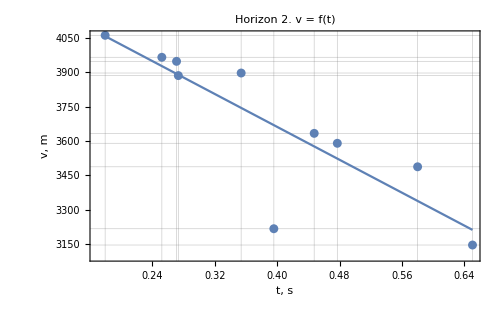
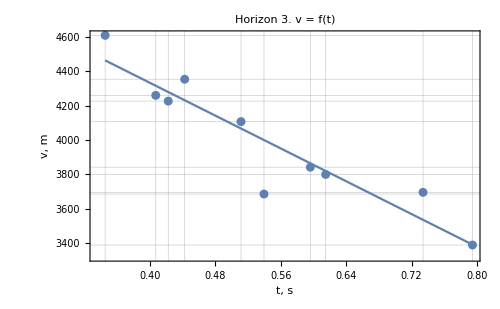
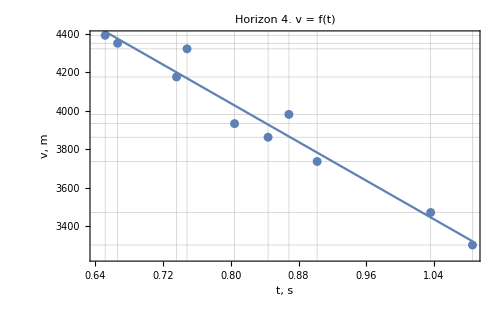

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[-0.0205846+0.000321383 h],FittedModel[-0.0765109+0.000333692 h],FittedModel[-0.242024+0.000369983 h],FittedModel[-0.895018+0.000532193 h]}

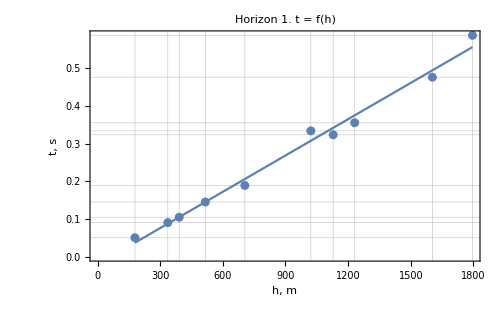
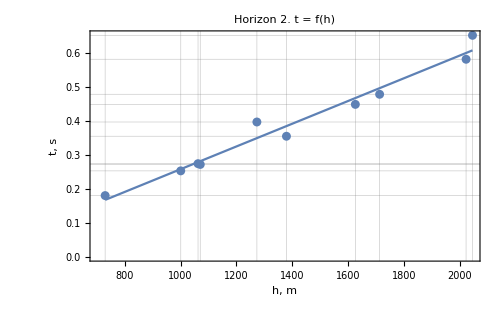
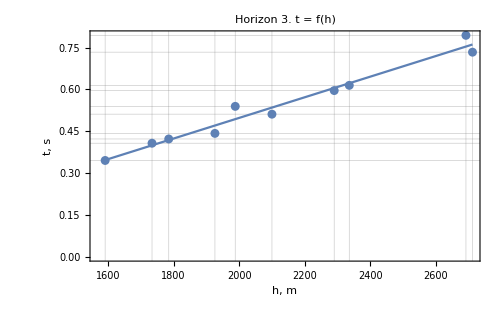
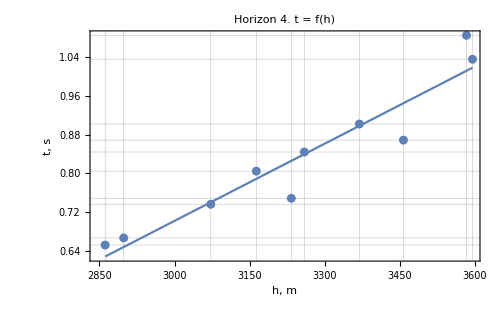

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{3473.09,3683.52,3996.72,3951.89}

{{{0,-356.158},{100,-314.231},{200,-318.136},{300,-363.73},{400,-466.585},{500,-588.218},{600,-709.795},{700,-792.252},{800,-830.748},{900,-865.073},{1000,-829.3},{1100,-766.181},{1200,-656.721},{1300,-630.441},{1400,-678.016},{1500,-763.301},{1600,-925.621},{1700,-1123.84},{1800,-1349.53},{1900,-1432.52},{2000,-1417.36},{2100,-1362.07},{2200,-1284.2},{2300,-1246.81},{2400,-1234.97},{2500,-1198.6},{2600,-1149.34},{2700,-1019.46},{2800,-890.785},{2900,-798.447},{3000,-715.614},{3100,-610.676},{3200,-574.042},{3300,-598.369},{3400,-665.877},{3500,-774.954},{3600,-884.235},{3700,-985.959},{3800,-1039.84},{3900,-996.775},{4000,-910.995},{4100,-881.973},{4200,-928.409},{4300,-1073.35},{4400,-1325.92},{4500,-1653.18},{4600,-1985.52},{4700,-2109.21},{4800,-1805.92},{4900,-1350.25},{5000,-964.532},{5100,-595.103},{5200,-349.827},{5300,-203.024},{5400,-93.6303},{5500,-99.1282},{5600,-134.175},{5700,-156.571},{5800,-196.555},{5900,-170.821},{6000,-174.806},{6100,-137.224},{6200,-166.491},{6300,-247.651},{6400,-435.197},{6500,-728.703},{6600,-971.892},{6700,-1166.35},{6800,-1160.26},{6900,-1013.33},{7000,-853.128},{7100,-704.499},{7200,-683.007},{7300,-737.911},{7400,-877.249},{7500,-1086.2},{7600,-1315.34},{7700,-1590.37},{7800,-1831.42},{7900,-2038.37},{8000,-2072.4},{8100,-2040.96},{8200,-1855.82},{8300,-1654.63},{8400,-1464.85},{8500,-1339.58},{8600,-1292.16},{8700,-1347.75},{8800,-1449.32},{8900,-1618.72},{9000,-1868.18},{9100,-1898.57},{9200,-1697.2},{9300,-1374.49},{9400,-1020.8},{9500,-757.401},{9600,-588.359},{9700,-504.135},{9800,-451.357},{9900,-366.073},{10000,-235.286}},{{0,-921.284},{100,-929.018},{200,-955.994},{300,-998.487},{400,-1060.72},{500,-1132.26},{600,-1207.35},{700,-1267.41},{800,-1305.21},{900,-1335.83},{1000,-1334.1},{1100,-1322.64},{1200,-1303.61},{1300,-1318.49},{1400,-1362.15},{1500,-1426.25},{1600,-1525.52},{1700,-1648.57},{1800,-1794.84},{1900,-1868.09},{2000,-1880.2},{2100,-1861.02},{2200,-1821.19},{2300,-1789.14},{2400,-1757.77},{2500,-1707.34},{2600,-1643.45},{2700,-1541.38},{2800,-1443.76},{2900,-1366.76},{3000,-1301.39},{3100,-1242.67},{3200,-1216.88},{3300,-1222.08},{3400,-1251.82},{3500,-1306.3},{3600,-1371.54},{3700,-1440.89},{3800,-1492.17},{3900,-1502.68},{4000,-1503.36},{4100,-1534.14},{4200,-1593.18},{4300,-1686.73},{4400,-1827.18},{4500,-2022.91},{4600,-2249.61},{4700,-2331.83},{4800,-2066.24},{4900,-1711.57},{5000,-1430.09},{5100,-1185.74},{5200,-1004.96},{5300,-864.882},{5400,-750.904},{5500,-679.452},{5600,-639.305},{5700,-619.665},{5800,-625.383},{5900,-631.473},{6000,-661.334},{6100,-697.574},{6200,-760.805},{6300,-842.841},{6400,-956.715},{6500,-1122.6},{6600,-1288.35},{6700,-1436.09},{6800,-1457.96},{6900,-1397.53},{7000,-1342.48},{7100,-1307.84},{7200,-1329.81},{7300,-1386.31},{7400,-1486.98},{7500,-1630.23},{7600,-1799.43},{7700,-2005.03},{7800,-2198.96},{7900,-2370.45},{8000,-2411.59},{8100,-2396.12},{8200,-2268.82},{8300,-2136.95},{8400,-2018.91},{8500,-1940.74},{8600,-1902.56},{8700,-1913.11},{8800,-1949.75},{8900,-2027.71},{9000,-2171.24},{9100,-2168.02},{9200,-1987.66},{9300,-1728.08},{9400,-1469.99},{9500,-1273.54},{9600,-1121.95},{9700,-1006.9},{9800,-910.952},{9900,-817.101},{10000,-725.298}},{{0,-1619.3},{100,-1627.23},{200,-1651.24},{300,-1688.36},{400,-1743.74},{500,-1810.25},{600,-1883.25},{700,-1944.3},{800,-1989.05},{900,-2032.21},{1000,-2045.55},{1100,-2050.5},{1200,-2043.92},{1300,-2069.18},{1400,-2118.},{1500,-2179.31},{1600,-2269.51},{1700,-2382.55},{1800,-2519.14},{1900,-2578.07},{2000,-2577.09},{2100,-2549.04},{2200,-2506.62},{2300,-2478.72},{2400,-2457.52},{2500,-2419.23},{2600,-2371.83},{2700,-2282.32},{2800,-2196.77},{2900,-2131.37},{3000,-2073.91},{3100,-2017.95},{3200,-1993.06},{3300,-1995.53},{3400,-2021.66},{3500,-2074.43},{3600,-2138.25},{3700,-2207.3},{3800,-2258.41},{3900,-2264.14},{4000,-2254.86},{4100,-2270.46},{4200,-2310.81},{4300,-2381.65},{4400,-2501.67},{4500,-2685.05},{4600,-2913.87},{4700,-3000.9},{4800,-2729.06},{4900,-2374.26},{5000,-2109.65},{5100,-1888.73},{5200,-1732.93},{5300,-1611.81},{5400,-1509.63},{5500,-1441.02},{5600,-1397.53},{5700,-1370.36},{5800,-1366.98},{5900,-1361.85},{6000,-1379.97},{6100,-1403.05},{6200,-1453.27},{6300,-1522.92},{6400,-1626.55},{6500,-1789.86},{6600,-1960.16},{6700,-2121.21},{6800,-2156.1},{6900,-2111.72},{7000,-2078.56},{7100,-2067.22},{7200,-2110.49},{7300,-2181.9},{7400,-2286.49},{7500,-2426.11},{7600,-2584.98},{7700,-2781.97},{7800,-2968.61},{7900,-3139.61},{8000,-3182.24},{8100,-3174.97},{8200,-3055.84},{8300,-2933.26},{8400,-2823.55},{8500,-2748.81},{8600,-2706.28},{8700,-2707.02},{8800,-2728.49},{8900,-2794.25},{9000,-2932.34},{9100,-2919.56},{9200,-2725.18},{9300,-2456.02},{9400,-2197.03},{9500,-2009.51},{9600,-1871.14},{9700,-1768.54},{9800,-1683.37},{9900,-1594.24},{10000,-1501.34}},{{0,-2565.39},{100,-2575.},{200,-2599.38},{300,-2633.06},{400,-2683.35},{500,-2742.93},{600,-2808.33},{700,-2860.76},{800,-2896.45},{900,-2929.37},{1000,-2933.08},{1100,-2926.36},{1200,-2908.18},{1300,-2920.53},{1400,-2955.19},{1500,-3001.83},{1600,-3078.83},{1700,-3178.98},{1800,-3305.86},{1900,-3362.61},{2000,-3364.7},{2100,-3348.49},{2200,-3324.75},{2300,-3322.7},{2400,-3335.44},{2500,-3335.76},{2600,-3329.95},{2700,-3285.34},{2800,-3241.97},{2900,-3214.21},{3000,-3189.92},{3100,-3158.66},{3200,-3148.03},{3300,-3154.88},{3400,-3176.16},{3500,-3211.7},{3600,-3249.72},{3700,-3287.07},{3800,-3300.36},{3900,-3264.55},{4000,-3213.7},{4100,-3193.09},{4200,-3199.29},{4300,-3246.05},{4400,-3351.92},{4500,-3535.45},{4600,-3776.12},{4700,-3893.25},{4800,-3669.22},{4900,-3375.41},{5000,-3181.91},{5100,-3036.18},{5200,-2958.48},{5300,-2913.55},{5400,-2882.68},{5500,-2877.07},{5600,-2887.69},{5700,-2900.32},{5800,-2925.13},{5900,-2934.66},{6000,-2957.09},{6100,-2975.25},{6200,-3011.25},{6300,-3061.02},{6400,-3141.15},{6500,-3278.01},{6600,-3419.74},{6700,-3553.87},{6800,-3564.39},{6900,-3495.65},{7000,-3437.16},{7100,-3400.53},{7200,-3417.22},{7300,-3459.02},{7400,-3531.95},{7500,-3641.35},{7600,-3770.72},{7700,-3937.48},{7800,-4103.01},{7900,-4256.53},{8000,-4293.21},{8100,-4289.45},{8200,-4187.41},{8300,-4094.25},{8400,-4027.36},{8500,-3974.26},{8600,-3951.9},{8700,-3960.64},{8800,-3994.9},{8900,-4086.96},{9000,-4259.29},{9100,-4287.11},{9200,-4139.69},{9300,-3922.99},{9400,-3718.09},{9500,-3580.37},{9600,-3490.84},{9700,-3432.67},{9800,-3382.09},{9900,-3319.51},{10000,-3244.22}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-